## Practical -3 Secant Method

Secant Method                                                                                                        
       To find a root of an equation using secant method in given number of iterations.
 (1)  Find a real root of the equation f(x)=x^3-5x+1=0 using secant method in six iterations.

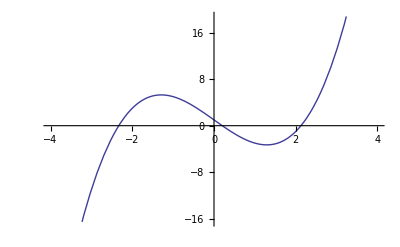

i | interval | xi | f[xi]
1 | [0.,1.] | 0.25 | -0.234375
2 | [1.,0.25] | 0.18644068 | 0.074277312
3 | [0.25,0.186440677966] | 0.20173626 | -0.00047111617
4 | [0.186440677966,0.201736256179] | 0.20163985 | -8.642293×10^-7
5 | [0.201736256179,0.201639852891] | 0.20163968 | 1.0352719×10^-11
6 | [0.201639852891,0.201639675721] | 0.20163968 | -2.220446×10^-16

Root after 6 iterrations 0.20163968

Function value at approximated root,f[xi]= -2.220446×10^-16

```mathematica
Secant[x0_,x1_,n_,f_]:=Module[{xk,xk1,xk2},xk=N[x0];xk1=N[x1];i=0;
Output={ };
While[i<n,xk2=(xk*f[xk1]-xk1*f[xk])/(f[xk1]-f[xk]);interval="["<>ToString[NumberForm[xk,12]]<>","<>ToString[NumberForm[xk1,12]]<>"]";xk=xk1;xk1=xk2;i++;
Output=Append[Output,{i,interval,xk2,f[xk2]}];];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"i","interval","xi","f[xi]"}}],8]];
Print[" Root after ",n," iterrations ",NumberForm[xk2,8]];
Print[" Function value at approximated root,f[xi]= ",NumberForm[f[xk2],8]];]
g[x_]:=x^3-5x+1;
Plot[g[x],{x,-4,4}]
Secant[0,1,6,g]
```

(2)  Find a real root of the equation f(x)=Cosx-xe^x using secant method in eight iterations

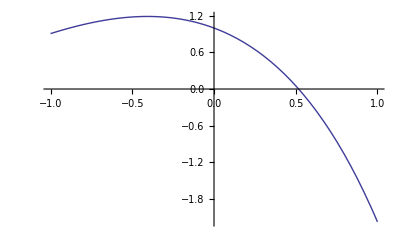

i | interval | xi | f[xi]
1 | [0.,1.] | 0.31466534 | 0.51987117
2 | [1.,0.314665337801] | 0.44672814 | 0.20354478
3 | [0.314665337801,0.446728144591] | 0.53170586 | -0.042931093
4 | [0.446728144591,0.531705860645] | 0.51690447 | 0.0025927631
5 | [0.531705860645,0.516904467567] | 0.51774747 | 0.000030111941
6 | [0.516904467567,0.517747465271] | 0.51775737 | -2.1513164×10^-8
7 | [0.517747465271,0.517757370754] | 0.51775736 | 1.7841284×10^-13
8 | [0.517757370754,0.517757363682] | 0.51775736 | -3.3306691×10^-16

Root after 8 iterrations 0.51775736

Function value at approximated root,f[xi]= -3.3306691×10^-16

```mathematica
f[x_]:=Cos[x]-x Exp[x];
Plot[f[x],{x,-1,1}]
Secant[0,1,8,f]
```